```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1035.53 ⅈ,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},{{1},12,{1}},297,{1},{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
Tally[{imp8,imp,imp2,imp10,imp4,imp2,imp,imp,imp,imp3,imp12,imp12,imp,imp4,imp,imp,imp,imp14,imp14,imp8,imp,imp13,imp9,imp,imp,imp,imp5,imp,imp6,imp6,imp,imp,imp,imp,imp,imp8,imp6,imp5,imp,imp,imp,imp7,imp,imp,imp13,imp,imp,imp14,imp3,imp3,imp,imp,imp,imp1,imp1,imp4,imp10,imp,imp,imp7,imp5,imp1,imp,imp3,imp,imp11,imp12,imp9,imp,imp11,imp5,imp2,imp2,imp14,imp13,imp,imp,imp,imp13,imp10,imp10,imp4,imp7,imp,imp9,imp,imp,imp12,imp,imp,imp,imp7,imp6,imp8,imp11,imp,imp9,imp1,imp,imp11}]
```

{{imp8,4},{imp,44},{imp2,4},{imp10,4},{imp4,4},{imp3,4},{imp12,4},{imp14,4},{imp13,4},{imp9,4},{imp5,4},{imp6,4},{imp7,4},{imp1,4},{imp11,4}}

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,3,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp]
```

```mathematica
RandomSample[Flatten[Join[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],2],Table[imp,72]]]]
```

{imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp6,imp10,imp,imp9,imp2,imp7,imp,imp1,imp,imp12,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp9,imp,imp3,imp,imp,imp4,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp3,imp,imp,imp8,imp11,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp12,imp7,imp,imp,imp,imp,imp13,imp}

```mathematica
Tally[{imp8,imp,imp2,imp10,imp4,imp2,imp,imp,imp,imp3,imp12,imp12,imp,imp4,imp,imp,imp,imp14,imp14,imp8,imp,imp13,imp9,imp,imp,imp,imp5,imp,imp6,imp6,imp,imp,imp,imp,imp,imp8,imp6,imp5,imp,imp,imp,imp7,imp,imp,imp13,imp,imp,imp14,imp3,imp3,imp,imp,imp,imp1,imp1,imp4,imp10,imp,imp,imp7,imp5,imp1,imp,imp3,imp,imp11,imp12,imp9,imp,imp11,imp5,imp2,imp2,imp14,imp13,imp,imp,imp,imp13,imp10,imp10,imp4,imp7,imp,imp9,imp,imp,imp12,imp,imp,imp,imp7,imp6,imp8,imp11,imp,imp9,imp1,imp,imp11}]
```

{{imp8,4},{imp,44},{imp2,4},{imp10,4},{imp4,4},{imp3,4},{imp12,4},{imp14,4},{imp13,4},{imp9,4},{imp5,4},{imp6,4},{imp7,4},{imp1,4},{imp11,4}}

```mathematica
Tally[{imp,imp,imp14,imp,imp9,imp,imp7,imp,imp3,imp,imp2,imp,imp,imp3,imp,imp8,imp,imp,imp7,imp,imp5,imp1,imp10,imp,imp,imp12,imp9,imp,imp5,imp13,imp7,imp,imp,imp,imp,imp2,imp,imp4,imp10,imp8,imp,imp,imp,imp6,imp,imp9,imp,imp11,imp,imp,imp,imp,imp12,imp,imp,imp5,imp,imp4,imp1,imp,imp,imp,imp6,imp10,imp6,imp,imp14,imp,imp12,imp1,imp,imp,imp,imp8,imp,imp4,imp,imp,imp14,imp,imp11,imp,imp,imp13,imp11,imp,imp,imp,imp,imp,imp,imp,imp2,imp13,imp,imp,imp,imp3,imp,imp}]
```

{{imp,58},{imp14,3},{imp9,3},{imp7,3},{imp3,3},{imp2,3},{imp8,3},{imp5,3},{imp1,3},{imp10,3},{imp12,3},{imp13,3},{imp4,3},{imp6,3},{imp11,3}}

```mathematica
misfit[ϵ1_,ϵ2_,y_,x_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={{imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp6,imp10,imp,imp9,imp2,imp7,imp,imp1,imp,imp12,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp9,imp,imp3,imp,imp,imp4,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp3,imp,imp,imp8,imp11,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp12,imp7,imp,imp,imp,imp,imp13,imp}};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
m5=Table[{ω,If[tra1>3,3,tra1]},{ω,Range[0,3,0.01]}];
v1=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]-Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_05t10.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_10t15.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_15t20.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_20t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_25t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_05_nb_30t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{0.5,0.5,Log[ρ2]^19},{0.5,1,Log[ρ3]^19},{0.5,1.5,Log[ρ4]^19},{0.5,2,Log[ρ5]^19},{0.5,2.5,Log[ρ6]^19},{0.5,3,Log[ρ7]^19}};
list];
v2=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_05t15.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_10t20.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_15t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_20t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_25t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_10_nb_30t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{1,0.5,Log[ρ2]^19},{1,1,Log[ρ3]^19},{1,1.5,Log[ρ4]^19},{1,2,Log[ρ5]^19},{1,2.5,Log[ρ6]^19},{1,3,Log[ρ7]^19}};
list];
v3=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_05t20.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_10t25.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_15t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_20t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_25t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_15_nb_30t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{1.50,.5,Log[ρ2]^19},{1.5,1,Log[ρ3]^19},{1.5,1.5,Log[ρ4]^19},{1.5,2,Log[ρ5]^19},{1.5,2.5,Log[ρ6]^19},{1.5,3,Log[ρ7]^19}};
list];
v4=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_05t25.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_10t30.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_15t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_20t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_25t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_20_nb_30t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2,.5,Log[ρ2]^19},{2,1,Log[ρ3]^19},{2,1.5,Log[ρ4]^19},{2,2,Log[ρ5]^19},{2,2.5,Log[ρ6]^19},{2,3,Log[ρ7]^19}};
list];
v5=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_05t30.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_10t35.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_15t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_20t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_25t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_25_nb_30t55.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{2.5,.5,Log[ρ2]^19},{2.5,1,Log[ρ3]^19},{2.5,1.5,Log[ρ4]^19},{2.5,2,Log[ρ5]^19},{2.5,2.5,Log[ρ6]^19},{2.5,3,Log[ρ7]^19}};
list];
v6=Module[{},
ρ2:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_05t35.dat"][[1;;150,;;]][[;;,2]])^2}]}, Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_10t40.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_15t45.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_20t50.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_25t55.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;150]][[;;,1]],(m5[[1;;150,2]]- Import["/home/shardul/PhD_new/PhD/fwi/AGNR/7AGNR/two_imp/na_30_nb_30t60.dat"][[1;;150,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list={{3,.5,Log[ρ2]^19},{3,1,Log[ρ3]^19},{3,1.5,Log[ρ4]^19},{3,2,Log[ρ5]^19},{3,2.5,Log[ρ6]^19},{3,3,Log[ρ7]^19}};
list];
aa={v1,v2,v3,v4,v5,v6};
{m5,
Join[(*aa[[1]],*)aa[[1]],aa[[2]],aa[[3]],aa[[4]],aa[[5]],aa[[6]](*,aa[[8]]*)(*,aa[[9]]*)]}]
```

```mathematica
ab=misfit[0.3,0.9,0.9,1.48]
ab[[Position[ab,Min[Transpose[ab][[3]]]][[1,1]]]]
```

{{{0.,2.80959×10^-7},{0.01,2.03097×10^-7},{0.02,2.85118×10^-8},{0.03,4.18707×10^-7},{0.04,9.80708×10^-7},{0.05,1.73712×10^-6},{0.06,2.72181×10^-6},{0.07,3.98282×10^-6},{0.08,5.58688×10^-6},{0.09,7.62611×10^-6},{0.1,0.0000102281},{0.11,0.0000135715},{0.12,0.0000179099},{0.13,0.0000236104},{0.14,0.0000312176},{0.15,0.0000415632},{0.16,0.000055964},{0.17,0.0000766017},{0.18,0.000107305},{0.19,0.000155328},{0.2,0.000235963},{0.21,0.000387058},{0.22,0.000731882},{0.23,0.00203366},{0.24,0.767023},{0.25,0.20007},{0.26,0.224464},{0.27,0.354799},{0.28,0.59808},{0.29,0.89741},{0.3,0.893928},{0.31,0.891566},{0.32,0.735272},{0.33,0.944437},{0.34,0.972311},{0.35,0.774291},{0.36,0.952877},{0.37,0.899906},{0.38,0.646569},{0.39,0.6921},{0.4,0.920812},{0.41,0.757809},{0.42,0.498872},{0.43,0.731838},{0.44,0.286163},{0.45,0.605},{0.46,0.613253},{0.47,0.771325},{0.48,1.5339},{0.49,0.344261},{0.5,0.918506},{0.51,0.0442704},{0.52,0.876344},{0.53,0.84834},{0.54,1.01102},{0.55,0.839532},{0.56,0.854257},{0.57,0.39246},{0.58,0.720599},{0.59,1.47449},{0.6,0.826752},{0.61,0.41005},{0.62,0.860349},{0.63,0.806105},{0.64,1.64489},{0.65,1.14213},{0.66,1.51191},{0.67,1.23332},{0.68,1.22662},{0.69,1.27056},{0.7,1.08304},{0.71,1.11644},{0.72,1.77685},{0.73,1.42109},{0.74,1.46967},{0.75,1.5366},{0.76,1.28494},{0.77,0.823099},{0.78,1.10652},{0.79,0.843113},{0.8,1.22979},{0.81,1.40143},{0.82,1.21873},{0.83,1.35116},{0.84,1.45693},{0.85,0.849558},{0.86,0.286373},{0.87,1.88947},{0.88,0.723845},{0.89,0.170885},{0.9,0.936102},{0.91,0.842713},{0.92,1.9301},{0.93,1.27498},{0.94,1.53394},{0.95,0.632541},{0.96,0.262464},{0.97,1.2008},{0.98,1.4866},{0.99,1.44533},{1.,1.38554},{1.01,1.20364},{1.02,1.9092},{1.03,1.14301},{1.04,0.658685},{1.05,0.284684},{1.06,1.49948},{1.07,1.32922},{1.08,1.11107},{1.09,0.0494514},{1.1,0.567315},{1.11,0.571294},{1.12,0.168562},{1.13,0.0405148},{1.14,0.868945},{1.15,0.941997},{1.16,0.745473},{1.17,0.957663},{1.18,0.856607},{1.19,0.450794},{1.2,0.188457},{1.21,0.501789},{1.22,0.191708},{1.23,0.723253},{1.24,0.391881},{1.25,1.13291},{1.26,0.873531},{1.27,1.00876},{1.28,0.424575},{1.29,1.27646},{1.3,1.25711},{1.31,1.04799},{1.32,0.73941},{1.33,0.095777},{1.34,0.929088},{1.35,1.10456},{1.36,1.19547},{1.37,1.14904},{1.38,1.03824},{1.39,0.68302},{1.4,1.09887},{1.41,0.293323},{1.42,0.732708},{1.43,1.49918},{1.44,1.44841},{1.45,1.40155},{1.46,0.678853},{1.47,0.785426},{1.48,0.718439},{1.49,0.868336},{1.5,0.870166},{1.51,1.02166},{1.52,1.41922},{1.53,1.47556},{1.54,0.10887},{1.55,1.66283},{1.56,0.278865},{1.57,1.33302},{1.58,0.589675},{1.59,0.090125},{1.6,0.637969},{1.61,1.13062},{1.62,1.01727},{1.63,0.638481},{1.64,0.798193},{1.65,0.0966832},{1.66,0.378348},{1.67,1.06962},{1.68,0.572257},{1.69,0.834699},{1.7,0.305223},{1.71,1.02229},{1.72,0.302932},{1.73,0.62007},{1.74,0.07566},{1.75,2.12295},{1.76,2.78714},{1.77,3},{1.78,0.31401},{1.79,0.0677526},{1.8,0.0253668},{1.81,0.19692},{1.82,0.0277777},{1.83,0.785599},{1.84,0.59035},{1.85,0.877246},{1.86,0.794957},{1.87,0.140495},{1.88,0.503327},{1.89,0.718877},{1.9,0.15406},{1.91,0.500279},{1.92,1.15268},{1.93,0.985466},{1.94,1.05469},{1.95,0.941895},{1.96,1.10468},{1.97,0.302977},{1.98,0.969385},{1.99,1.00295},{2.,0.4874},{2.01,0.46717},{2.02,0.709664},{2.03,0.385408},{2.04,1.2991},{2.05,0.683465},{2.06,0.128035},{2.07,0.411825},{2.08,1.37338},{2.09,0.321894},{2.1,0.629801},{2.11,0.0664517},{2.12,1.10218},{2.13,1.13034},{2.14,0.879084},{2.15,0.651274},{2.16,0.740748},{2.17,1.04246},{2.18,0.535992},{2.19,0.233502},{2.2,0.294347},{2.21,0.43567},{2.22,0.633436},{2.23,0.885739},{2.24,0.362406},{2.25,0.590738},{2.26,0.523489},{2.27,0.225979},{2.28,0.321794},{2.29,0.801077},{2.3,0.830209},{2.31,0.358471},{2.32,0.462272},{2.33,0.420047},{2.34,0.181679},{2.35,0.204112},{2.36,0.543664},{2.37,0.932668},{2.38,0.634128},{2.39,0.169888},{2.4,0.116824},{2.41,0.47636},{2.42,0.136444},{2.43,3},{2.44,0.705366},{2.45,0.882628},{2.46,0.0266637},{2.47,0.013372},{2.48,0.00444891},{2.49,0.00630791},{2.5,0.00820059},{2.51,0.00741325},{2.52,0.0060804},{2.53,0.0750436},{2.54,0.563535},{2.55,0.0985788},{2.56,0.0608449},{2.57,0.0567799},{2.58,0.101181},{2.59,0.237216},{2.6,0.0543624},{2.61,0.857743},{2.62,0.0269654},{2.63,0.050021},{2.64,0.0289501},{2.65,0.0268112},{2.66,0.0369193},{2.67,0.0248331},{2.68,0.465648},{2.69,0.0196103},{2.7,0.11963},{2.71,0.324944},{2.72,0.252036},{2.73,0.0810037},{2.74,0.305694},{2.75,0.0440526},{2.76,0.0192735},{2.77,0.17512},{2.78,0.0173881},{2.79,0.0150414},{2.8,0.214351},{2.81,0.0470219},{2.82,0.055978},{2.83,0.0067598},{2.84,0.0571026},{2.85,0.0000699581},{2.86,0.0000596933},{2.87,0.0000687984},{2.88,0.0000710472},{2.89,0.000282283},{2.9,0.0127985},{2.91,0.0000895181},{2.92,0.0000174275},{2.93,5.62014×10^-6},{2.94,2.22665×10^-6},{2.95,9.71326×10^-7},{2.96,4.36051×10^-7},{2.97,1.86998×10^-7},{2.98,6.47876×10^-8},{2.99,3.18801×10^-9},{3.,2.78624×10^-8}},{{0.5,0.5,-1.83412×10^15},{0.5,1,-3.095×10^16},{0.5,1.5,-1.67626×10^16},{0.5,2,-8.40714×10^15},{0.5,2.5,-4.92236×10^15},{0.5,3,-3.33525×10^15},{1,0.5,-7.74035×10^15},{1,1,-3.13741×10^16},{1,1.5,-2.94748×10^16},{1,2,-5.32341×10^15},{1,2.5,-3.00753×10^15},{1,3,-3.55977×10^15},{1.5,0.5,-4.06462×10^15},{1.5,1,-1.87696×10^16},{1.5,1.5,-1.37765×10^16},{1.5,2,-8.21892×10^15},{1.5,2.5,-2.89855×10^15},{1.5,3,-2.11071×10^15},{2,0.5,-2.84259×10^15},{2,1,-2.77991×10^16},{2,1.5,-1.68281×10^16},{2,2,-5.65513×10^15},{2,2.5,-2.69485×10^15},{2,3,-2.06979×10^15},{2.5,0.5,-4.23712×10^15},{2.5,1,-2.45363×10^16},{2.5,1.5,-8.63606×10^15},{2.5,2,-4.08071×10^15},{2.5,2.5,-3.42955×10^15},{2.5,3,-2.05803×10^15},{3,0.5,-6.20524×10^15},{3,1,-2.70167×10^16},{3,1.5,-7.74364×10^15},{3,2,-3.82791×10^15},{3,2.5,-2.49523×10^15},{3,3,-2.48968×10^15}}}

Transpose::nmtx: The first two levels of {{{0.,2.80959×10^-7},{0.01,2.03097×10^-7},{0.02,2.85118×10^-8},{0.03,4.18707×10^-7},{0.04,9.80708×10^-7},{0.05,1.73712×10^-6},{0.06,2.72181×10^-6},{0.07,3.98282×10^-6},{0.08,5.58688×10^-6},{0.09,7.62611×10^-6},«291»},{{0.5,0.5,-1.83412×10^15},{0.5,1,-3.095×10^16},{0.5,1.5,-1.67626×10^16},{0.5,2,-8.40714×10^15},{0.5,2.5,-4.92236×10^15},{0.5,3,-3.33525×10^15},{1,0.5,-7.74035×10^15},{1,1,-3.13741×10^16},{1,1.5,-2.94748×10^16},{1,2,-5.32341×10^15},«26»}} cannot be transposed.

Part::partw: Part 3 of Transpose[{{{0.,2.80959×10^-7},{0.01,2.03097×10^-7},{0.02,2.85118×10^-8},{0.03,4.18707×10^-7},{0.04,9.80708×10^-7},{0.05,1.73712×10^-6},{0.06,2.72181×10^-6},{0.07,3.98282×10^-6},{0.08,5.58688×10^-6},{0.09,7.62611×10^-6},«291»},{{0.5,0.5,-1.83412×10^15},{0.5,1,-3.095×10^16},{0.5,1.5,-1.67626×10^16},{0.5,2,-8.40714×10^15},{0.5,2.5,-4.92236×10^15},{0.5,3,-3.33525×10^15},{1,0.5,-7.74035×10^15},{1,1,-3.13741×10^16},{1,1.5,-2.94748×10^16},{1,2,-5.32341×10^15},«26»}}] does not exist.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{{0.,2.80959×10^-7},{0.01,2.03097×10^-7},{0.02,2.85118×10^-8},{0.03,4.18707×10^-7},{0.04,9.80708×10^-7},{0.05,1.73712×10^-6},{0.06,2.72181×10^-6},{0.07,3.98282×10^-6},{0.08,5.58688×10^-6},{0.09,7.62611×10^-6},{0.1,0.0000102281},{0.11,0.0000135715},{0.12,0.0000179099},{0.13,0.0000236104},{0.14,0.0000312176},{0.15,0.0000415632},{0.16,0.000055964},{0.17,0.0000766017},{0.18,0.000107305},{0.19,0.000155328},{0.2,0.000235963},{0.21,0.000387058},{0.22,0.000731882},{0.23,0.00203366},{0.24,0.767023},{0.25,0.20007},{0.26,0.224464},{0.27,0.354799},{0.28,0.59808},{0.29,0.89741},{0.3,0.893928},{0.31,0.891566},{0.32,0.735272},{0.33,0.944437},{0.34,0.972311},{0.35,0.774291},{0.36,0.952877},{0.37,0.899906},{0.38,0.646569},{0.39,0.6921},{0.4,0.920812},{0.41,0.757809},{0.42,0.498872},{0.43,0.731838},{0.44,0.286163},{0.45,0.605},{0.46,0.613253},{0.47,0.771325},{0.48,1.5339},{0.49,0.344261},{0.5,0.918506},{0.51,0.0442704},{0.52,0.876344},{0.53,0.84834},{0.54,1.01102},{0.55,0.839532},{0.56,0.854257},{0.57,0.39246},{0.58,0.720599},{0.59,1.47449},{0.6,0.826752},{0.61,0.41005},{0.62,0.860349},{0.63,0.806105},{0.64,1.64489},{0.65,1.14213},{0.66,1.51191},{0.67,1.23332},{0.68,1.22662},{0.69,1.27056},{0.7,1.08304},{0.71,1.11644},{0.72,1.77685},{0.73,1.42109},{0.74,1.46967},{0.75,1.5366},{0.76,1.28494},{0.77,0.823099},{0.78,1.10652},{0.79,0.843113},{0.8,1.22979},{0.81,1.40143},{0.82,1.21873},{0.83,1.35116},{0.84,1.45693},{0.85,0.849558},{0.86,0.286373},{0.87,1.88947},{0.88,0.723845},{0.89,0.170885},{0.9,0.936102},{0.91,0.842713},{0.92,1.9301},{0.93,1.27498},{0.94,1.53394},{0.95,0.632541},{0.96,0.262464},{0.97,1.2008},{0.98,1.4866},{0.99,1.44533},{1.,1.38554},{1.01,1.20364},{1.02,1.9092},{1.03,1.14301},{1.04,0.658685},{1.05,0.284684},{1.06,1.49948},{1.07,1.32922},{1.08,1.11107},{1.09,0.0494514},{1.1,0.567315},{1.11,0.571294},{1.12,0.168562},{1.13,0.0405148},{1.14,0.868945},{1.15,0.941997},{1.16,0.745473},{1.17,0.957663},{1.18,0.856607},{1.19,0.450794},{1.2,0.188457},{1.21,0.501789},{1.22,0.191708},{1.23,0.723253},{1.24,0.391881},{1.25,1.13291},{1.26,0.873531},{1.27,1.00876},{1.28,0.424575},{1.29,1.27646},{1.3,1.25711},{1.31,1.04799},{1.32,0.73941},{1.33,0.095777},{1.34,0.929088},{1.35,1.10456},{1.36,1.19547},{1.37,1.14904},{1.38,1.03824},{1.39,0.68302},{1.4,1.09887},{1.41,0.293323},{1.42,0.732708},{1.43,1.49918},{1.44,1.44841},{1.45,1.40155},{1.46,0.678853},{1.47,0.785426},{1.48,0.718439},{1.49,0.868336},{1.5,0.870166},{1.51,1.02166},{1.52,1.41922},{1.53,1.47556},{1.54,0.10887},{1.55,1.66283},{1.56,0.278865},{1.57,1.33302},{1.58,0.589675},{1.59,0.090125},{1.6,0.637969},{1.61,1.13062},{1.62,1.01727},{1.63,0.638481},{1.64,0.798193},{1.65,0.0966832},{1.66,0.378348},{1.67,1.06962},{1.68,0.572257},{1.69,0.834699},{1.7,0.305223},{1.71,1.02229},{1.72,0.302932},{1.73,0.62007},{1.74,0.07566},{1.75,2.12295},{1.76,2.78714},{1.77,3},{1.78,0.31401},{1.79,0.0677526},{1.8,0.0253668},{1.81,0.19692},{1.82,0.0277777},{1.83,0.785599},{1.84,0.59035},{1.85,0.877246},{1.86,0.794957},{1.87,0.140495},{1.88,0.503327},{1.89,0.718877},{1.9,0.15406},{1.91,0.500279},{1.92,1.15268},{1.93,0.985466},{1.94,1.05469},{1.95,0.941895},{1.96,1.10468},{1.97,0.302977},{1.98,0.969385},{1.99,1.00295},{2.,0.4874},{2.01,0.46717},{2.02,0.709664},{2.03,0.385408},{2.04,1.2991},{2.05,0.683465},{2.06,0.128035},{2.07,0.411825},{2.08,1.37338},{2.09,0.321894},{2.1,0.629801},{2.11,0.0664517},{2.12,1.10218},{2.13,1.13034},{2.14,0.879084},{2.15,0.651274},{2.16,0.740748},{2.17,1.04246},{2.18,0.535992},{2.19,0.233502},{2.2,0.294347},{2.21,0.43567},{2.22,0.633436},{2.23,0.885739},{2.24,0.362406},{2.25,0.590738},{2.26,0.523489},{2.27,0.225979},{2.28,0.321794},{2.29,0.801077},{2.3,0.830209},{2.31,0.358471},{2.32,0.462272},{2.33,0.420047},{2.34,0.181679},{2.35,0.204112},{2.36,0.543664},{2.37,0.932668},{2.38,0.634128},{2.39,0.169888},{2.4,0.116824},{2.41,0.47636},{2.42,0.136444},{2.43,3},{2.44,0.705366},{2.45,0.882628},{2.46,0.0266637},{2.47,0.013372},{2.48,0.00444891},{2.49,0.00630791},{2.5,0.00820059},{2.51,0.00741325},{2.52,0.0060804},{2.53,0.0750436},{2.54,0.563535},{2.55,0.0985788},{2.56,0.0608449},{2.57,0.0567799},{2.58,0.101181},{2.59,0.237216},{2.6,0.0543624},{2.61,0.857743},{2.62,0.0269654},{2.63,0.050021},{2.64,0.0289501},{2.65,0.0268112},{2.66,0.0369193},{2.67,0.0248331},{2.68,0.465648},{2.69,0.0196103},{2.7,0.11963},{2.71,0.324944},{2.72,0.252036},{2.73,0.0810037},{2.74,0.305694},{2.75,0.0440526},{2.76,0.0192735},{2.77,0.17512},{2.78,0.0173881},{2.79,0.0150414},{2.8,0.214351},{2.81,0.0470219},{2.82,0.055978},{2.83,0.0067598},{2.84,0.0571026},{2.85,0.0000699581},{2.86,0.0000596933},{2.87,0.0000687984},{2.88,0.0000710472},{2.89,0.000282283},{2.9,0.0127985},{2.91,0.0000895181},{2.92,0.0000174275},{2.93,5.62014×10^-6},{2.94,2.22665×10^-6},{2.95,9.71326×10^-7},{2.96,4.36051×10^-7},{2.97,1.86998×10^-7},{2.98,6.47876×10^-8},{2.99,3.18801×10^-9},{3.,2.78624×10^-8}},{{0.5,0.5,-1.83412×10^15},{0.5,1,-3.095×10^16},{0.5,1.5,-1.67626×10^16},{0.5,2,-8.40714×10^15},{0.5,2.5,-4.92236×10^15},{0.5,3,-3.33525×10^15},{1,0.5,-7.74035×10^15},{1,1,-3.13741×10^16},{1,1.5,-2.94748×10^16},{1,2,-5.32341×10^15},{1,2.5,-3.00753×10^15},{1,3,-3.55977×10^15},{1.5,0.5,-4.06462×10^15},{1.5,1,-1.87696×10^16},{1.5,1.5,-1.37765×10^16},{1.5,2,-8.21892×10^15},{1.5,2.5,-2.89855×10^15},{1.5,3,-2.11071×10^15},{2,0.5,-2.84259×10^15},{2,1,-2.77991×10^16},{2,1.5,-1.68281×10^16},{2,2,-5.65513×10^15},{2,2.5,-2.69485×10^15},{2,3,-2.06979×10^15},{2.5,0.5,-4.23712×10^15},{2.5,1,-2.45363×10^16},{2.5,1.5,-8.63606×10^15},{2.5,2,-4.08071×10^15},{2.5,2.5,-3.42955×10^15},{2.5,3,-2.05803×10^15},{3,0.5,-6.20524×10^15},{3,1,-2.70167×10^16},{3,1.5,-7.74364×10^15},{3,2,-3.82791×10^15},{3,2.5,-2.49523×10^15},{3,3,-2.48968×10^15}}}⟦{}⟦1,1⟧⟧

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/transmission_nanb.dat",ab[[1]]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/transmission_nanb.dat

```mathematica
ab=misfit[0.3,0.9,0.8,1.48]
Position[ab,Min[Transpose[ab][[3]]]]
cd={ab[[Position[ab,Min[Transpose[ab][[3]]]][[1,1]],1]],ab[[Position[ab,Min[Transpose[ab][[3]]]][[1,1]],2]]}
GraphicsRow[{Plot3D[Interpolation[ab,InterpolationOrder->3][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{cd[[1]],y},{y,Range[0,5.5,0.075]}],Table[{y,cd[[2]]},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]]}]
```

{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},{0.1,0.0000102448},{0.11,0.0000136003},{0.12,0.0000179574},{0.13,0.0000236875},{0.14,0.0000313423},{0.15,0.0000417668},{0.16,0.0000563031},{0.17,0.000077185},{0.18,0.000108356},{0.19,0.000157357},{0.2,0.000240294},{0.21,0.00039792},{0.22,0.000768481},{0.23,0.00229817},{0.24,0.216927},{0.25,0.387597},{0.26,0.164882},{0.27,0.445111},{0.28,0.691001},{0.29,0.496696},{0.3,0.749193},{0.31,0.85401},{0.32,0.624885},{0.33,0.832767},{0.34,0.550469},{0.35,0.663215},{0.36,0.950048},{0.37,0.884751},{0.38,0.847202},{0.39,0.972901},{0.4,0.942017},{0.41,0.834322},{0.42,0.336554},{0.43,1.44491},{0.44,0.856469},{0.45,0.083446},{0.46,0.57304},{0.47,1.05329},{0.48,1.60849},{0.49,1.47911},{0.5,1.0428},{0.51,0.090086},{0.52,0.963878},{0.53,0.957564},{0.54,0.866903},{0.55,1.25895},{0.56,1.54931},{0.57,1.35652},{0.58,1.18558},{0.59,1.21389},{0.6,1.4283},{0.61,1.32803},{0.62,1.11592},{0.63,1.77463},{0.64,1.67529},{0.65,1.60314},{0.66,1.43176},{0.67,1.52783},{0.68,1.31458},{0.69,1.41996},{0.7,1.2935},{0.71,1.73376},{0.72,1.46693},{0.73,1.2315},{0.74,1.74714},{0.75,0.993757},{0.76,1.85733},{0.77,1.29397},{0.78,1.65869},{0.79,1.48526},{0.8,1.46963},{0.81,0.980024},{0.82,1.22328},{0.83,1.6414},{0.84,1.47775},{0.85,1.52686},{0.86,1.18167},{0.87,0.99799},{0.88,1.44687},{0.89,0.695923},{0.9,1.6311},{0.91,2.44816},{0.92,1.95523},{0.93,1.8964},{0.94,1.82912},{0.95,2.05028},{0.96,2.23159},{0.97,1.78782},{0.98,2.22437},{0.99,2.1971},{1.,2.53763},{1.01,2.33047},{1.02,2.62338},{1.03,1.10436},{1.04,0.552345},{1.05,1.02696},{1.06,0.982417},{1.07,0.946522},{1.08,0.285907},{1.09,0.496167},{1.1,0.229481},{1.11,0.0575298},{1.12,0.560662},{1.13,0.259636},{1.14,0.372884},{1.15,0.648611},{1.16,0.178415},{1.17,0.166362},{1.18,0.35331},{1.19,0.166442},{1.2,0.290843},{1.21,0.609885},{1.22,0.709761},{1.23,0.779594},{1.24,0.375345},{1.25,0.557654},{1.26,0.0762372},{1.27,0.122151},{1.28,0.461555},{1.29,0.730922},{1.3,0.908008},{1.31,1.09487},{1.32,1.01055},{1.33,0.817678},{1.34,1.59891},{1.35,0.676413},{1.36,1.02354},{1.37,0.396917},{1.38,0.876227},{1.39,1.25222},{1.4,0.598531},{1.41,0.466878},{1.42,1.16808},{1.43,0.849554},{1.44,1.71903},{1.45,0.889551},{1.46,1.45363},{1.47,0.971954},{1.48,1.84261},{1.49,0.796133},{1.5,0.707813},{1.51,0.431887},{1.52,1.06981},{1.53,1.04284},{1.54,0.94024},{1.55,0.597348},{1.56,0.850695},{1.57,0.759401},{1.58,0.85398},{1.59,0.593154},{1.6,1.25327},{1.61,0.50345},{1.62,1.29707},{1.63,0.261118},{1.64,0.593374},{1.65,0.586208},{1.66,0.473518},{1.67,0.547705},{1.68,0.771237},{1.69,0.0570962},{1.7,0.408263},{1.71,0.180799},{1.72,1.20463},{1.73,0.324946},{1.74,0.335948},{1.75,0.492582},{1.76,3},{1.77,3},{1.78,0.300981},{1.79,0.891639},{1.8,0.654585},{1.81,0.37143},{1.82,0.498834},{1.83,0.304568},{1.84,0.292682},{1.85,0.366231},{1.86,0.257645},{1.87,0.468503},{1.88,0.359995},{1.89,0.408161},{1.9,0.766882},{1.91,1.28226},{1.92,1.51803},{1.93,1.38021},{1.94,1.02536},{1.95,0.624062},{1.96,0.409822},{1.97,0.766376},{1.98,1.69557},{1.99,0.795055},{2.,0.590642},{2.01,1.10575},{2.02,0.868901},{2.03,0.349633},{2.04,1.11136},{2.05,0.403938},{2.06,1.04969},{2.07,0.40505},{2.08,0.893945},{2.09,0.822431},{2.1,0.588702},{2.11,0.811988},{2.12,0.591675},{2.13,0.629576},{2.14,0.546622},{2.15,1.02357},{2.16,0.800782},{2.17,0.349538},{2.18,0.573084},{2.19,0.627126},{2.2,0.355827},{2.21,0.252076},{2.22,0.476152},{2.23,0.83757},{2.24,0.111031},{2.25,0.579684},{2.26,0.818858},{2.27,0.146705},{2.28,0.893762},{2.29,0.840723},{2.3,0.211563},{2.31,0.692802},{2.32,0.745316},{2.33,0.904567},{2.34,0.919804},{2.35,0.468059},{2.36,0.441173},{2.37,0.722231},{2.38,0.15698},{2.39,0.611515},{2.4,0.270506},{2.41,0.427276},{2.42,3},{2.43,2.84888},{2.44,3},{2.45,0.0216368},{2.46,0.0252919},{2.47,0.00012527},{2.48,0.0129467},{2.49,0.0417332},{2.5,0.0473329},{2.51,0.446482},{2.52,0.0126762},{2.53,0.148202},{2.54,0.116444},{2.55,0.417807},{2.56,0.294575},{2.57,0.0345147},{2.58,0.215416},{2.59,0.189494},{2.6,0.387526},{2.61,0.0480484},{2.62,0.0640367},{2.63,0.268065},{2.64,0.0651347},{2.65,0.0713828},{2.66,0.321127},{2.67,0.041942},{2.68,0.090806},{2.69,0.060038},{2.7,0.122481},{2.71,0.0833133},{2.72,0.263099},{2.73,0.0505861},{2.74,0.184303},{2.75,0.309661},{2.76,0.0354483},{2.77,0.207943},{2.78,0.0123986},{2.79,0.0118829},{2.8,0.0221652},{2.81,0.0707076},{2.82,0.898582},{2.83,0.00604876},{2.84,0.00312023},{2.85,0.000067071},{2.86,0.0000574759},{2.87,0.0000643502},{2.88,0.0000990633},{2.89,0.000313204},{2.9,0.00322995},{2.91,0.0000905209},{2.92,0.0000174475},{2.93,5.62145×10^-6},{2.94,2.22679×10^-6},{2.95,9.71347×10^-7},{2.96,4.36055×10^-7},{2.97,1.86999×10^-7},{2.98,6.47877×10^-8},{2.99,3.18804×10^-9},{3.,2.78624×10^-8}},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},{1,2.5,-4.17285×10^14},{1,3,-5.67835×10^14},{1.5,0.5,-3.79614×10^15},{1.5,1,-3.88181×10^15},{1.5,1.5,-2.28642×10^15},{1.5,2,-1.43116×10^15},{1.5,2.5,-3.97166×10^14},{1.5,3,-2.87513×10^14},{2,0.5,-2.6427×10^15},{2,1,-5.00678×10^15},{2,1.5,-3.29271×10^15},{2,2,-8.40567×10^14},{2,2.5,-3.72779×10^14},{2,3,-2.76878×10^14},{2.5,0.5,-3.27738×10^15},{2.5,1,-4.01863×10^15},{2.5,1.5,-1.20746×10^15},{2.5,2,-5.69346×10^14},{2.5,2.5,-5.07509×10^14},{2.5,3,-2.67582×10^14},{3,0.5,-3.78278×10^15},{3,1,-6.13522×10^15},{3,1.5,-1.05853×10^15},{3,2,-5.1656×10^14},{3,2.5,-3.36716×10^14},{3,3,-3.55656×10^14}}}

Transpose::nmtx: The first two levels of {{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}} cannot be transposed.

Part::partw: Part 3 of Transpose[{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}}] does not exist.

{}

Transpose::nmtx: The first two levels of {{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}} cannot be transposed.

Part::partw: Part 3 of Transpose[{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}}] does not exist.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Transpose::nmtx: The first two levels of {{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}} cannot be transposed.

Part::partw: Part 3 of Transpose[{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},«291»},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},{0.1,0.0000102448},{0.11,0.0000136003},{0.12,0.0000179574},{0.13,0.0000236875},{0.14,0.0000313423},{0.15,0.0000417668},{0.16,0.0000563031},{0.17,0.000077185},{0.18,0.000108356},{0.19,0.000157357},{0.2,0.000240294},{0.21,0.00039792},{0.22,0.000768481},{0.23,0.00229817},{0.24,0.216927},{0.25,0.387597},{0.26,0.164882},{0.27,0.445111},{0.28,0.691001},{0.29,0.496696},{0.3,0.749193},{0.31,0.85401},{0.32,0.624885},{0.33,0.832767},{0.34,0.550469},{0.35,0.663215},{0.36,0.950048},{0.37,0.884751},{0.38,0.847202},{0.39,0.972901},{0.4,0.942017},{0.41,0.834322},{0.42,0.336554},{0.43,1.44491},{0.44,0.856469},{0.45,0.083446},{0.46,0.57304},{0.47,1.05329},{0.48,1.60849},{0.49,1.47911},{0.5,1.0428},{0.51,0.090086},{0.52,0.963878},{0.53,0.957564},{0.54,0.866903},{0.55,1.25895},{0.56,1.54931},{0.57,1.35652},{0.58,1.18558},{0.59,1.21389},{0.6,1.4283},{0.61,1.32803},{0.62,1.11592},{0.63,1.77463},{0.64,1.67529},{0.65,1.60314},{0.66,1.43176},{0.67,1.52783},{0.68,1.31458},{0.69,1.41996},{0.7,1.2935},{0.71,1.73376},{0.72,1.46693},{0.73,1.2315},{0.74,1.74714},{0.75,0.993757},{0.76,1.85733},{0.77,1.29397},{0.78,1.65869},{0.79,1.48526},{0.8,1.46963},{0.81,0.980024},{0.82,1.22328},{0.83,1.6414},{0.84,1.47775},{0.85,1.52686},{0.86,1.18167},{0.87,0.99799},{0.88,1.44687},{0.89,0.695923},{0.9,1.6311},{0.91,2.44816},{0.92,1.95523},{0.93,1.8964},{0.94,1.82912},{0.95,2.05028},{0.96,2.23159},{0.97,1.78782},{0.98,2.22437},{0.99,2.1971},{1.,2.53763},{1.01,2.33047},{1.02,2.62338},{1.03,1.10436},{1.04,0.552345},{1.05,1.02696},{1.06,0.982417},{1.07,0.946522},{1.08,0.285907},{1.09,0.496167},{1.1,0.229481},{1.11,0.0575298},{1.12,0.560662},{1.13,0.259636},{1.14,0.372884},{1.15,0.648611},{1.16,0.178415},{1.17,0.166362},{1.18,0.35331},{1.19,0.166442},{1.2,0.290843},{1.21,0.609885},{1.22,0.709761},{1.23,0.779594},{1.24,0.375345},{1.25,0.557654},{1.26,0.0762372},{1.27,0.122151},{1.28,0.461555},{1.29,0.730922},{1.3,0.908008},{1.31,1.09487},{1.32,1.01055},{1.33,0.817678},{1.34,1.59891},{1.35,0.676413},{1.36,1.02354},{1.37,0.396917},{1.38,0.876227},{1.39,1.25222},{1.4,0.598531},{1.41,0.466878},{1.42,1.16808},{1.43,0.849554},{1.44,1.71903},{1.45,0.889551},{1.46,1.45363},{1.47,0.971954},{1.48,1.84261},{1.49,0.796133},{1.5,0.707813},{1.51,0.431887},{1.52,1.06981},{1.53,1.04284},{1.54,0.94024},{1.55,0.597348},{1.56,0.850695},{1.57,0.759401},{1.58,0.85398},{1.59,0.593154},{1.6,1.25327},{1.61,0.50345},{1.62,1.29707},{1.63,0.261118},{1.64,0.593374},{1.65,0.586208},{1.66,0.473518},{1.67,0.547705},{1.68,0.771237},{1.69,0.0570962},{1.7,0.408263},{1.71,0.180799},{1.72,1.20463},{1.73,0.324946},{1.74,0.335948},{1.75,0.492582},{1.76,3},{1.77,3},{1.78,0.300981},{1.79,0.891639},{1.8,0.654585},{1.81,0.37143},{1.82,0.498834},{1.83,0.304568},{1.84,0.292682},{1.85,0.366231},{1.86,0.257645},{1.87,0.468503},{1.88,0.359995},{1.89,0.408161},{1.9,0.766882},{1.91,1.28226},{1.92,1.51803},{1.93,1.38021},{1.94,1.02536},{1.95,0.624062},{1.96,0.409822},{1.97,0.766376},{1.98,1.69557},{1.99,0.795055},{2.,0.590642},{2.01,1.10575},{2.02,0.868901},{2.03,0.349633},{2.04,1.11136},{2.05,0.403938},{2.06,1.04969},{2.07,0.40505},{2.08,0.893945},{2.09,0.822431},{2.1,0.588702},{2.11,0.811988},{2.12,0.591675},{2.13,0.629576},{2.14,0.546622},{2.15,1.02357},{2.16,0.800782},{2.17,0.349538},{2.18,0.573084},{2.19,0.627126},{2.2,0.355827},{2.21,0.252076},{2.22,0.476152},{2.23,0.83757},{2.24,0.111031},{2.25,0.579684},{2.26,0.818858},{2.27,0.146705},{2.28,0.893762},{2.29,0.840723},{2.3,0.211563},{2.31,0.692802},{2.32,0.745316},{2.33,0.904567},{2.34,0.919804},{2.35,0.468059},{2.36,0.441173},{2.37,0.722231},{2.38,0.15698},{2.39,0.611515},{2.4,0.270506},{2.41,0.427276},{2.42,3},{2.43,2.84888},{2.44,3},{2.45,0.0216368},{2.46,0.0252919},{2.47,0.00012527},{2.48,0.0129467},{2.49,0.0417332},{2.5,0.0473329},{2.51,0.446482},{2.52,0.0126762},{2.53,0.148202},{2.54,0.116444},{2.55,0.417807},{2.56,0.294575},{2.57,0.0345147},{2.58,0.215416},{2.59,0.189494},{2.6,0.387526},{2.61,0.0480484},{2.62,0.0640367},{2.63,0.268065},{2.64,0.0651347},{2.65,0.0713828},{2.66,0.321127},{2.67,0.041942},{2.68,0.090806},{2.69,0.060038},{2.7,0.122481},{2.71,0.0833133},{2.72,0.263099},{2.73,0.0505861},{2.74,0.184303},{2.75,0.309661},{2.76,0.0354483},{2.77,0.207943},{2.78,0.0123986},{2.79,0.0118829},{2.8,0.0221652},{2.81,0.0707076},{2.82,0.898582},{2.83,0.00604876},{2.84,0.00312023},{2.85,0.000067071},{2.86,0.0000574759},{2.87,0.0000643502},{2.88,0.0000990633},{2.89,0.000313204},{2.9,0.00322995},{2.91,0.0000905209},{2.92,0.0000174475},{2.93,5.62145×10^-6},{2.94,2.22679×10^-6},{2.95,9.71347×10^-7},{2.96,4.36055×10^-7},{2.97,1.86999×10^-7},{2.98,6.47877×10^-8},{2.99,3.18804×10^-9},{3.,2.78624×10^-8}},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},{1,2.5,-4.17285×10^14},{1,3,-5.67835×10^14},{1.5,0.5,-3.79614×10^15},{1.5,1,-3.88181×10^15},{1.5,1.5,-2.28642×10^15},{1.5,2,-1.43116×10^15},{1.5,2.5,-3.97166×10^14},{1.5,3,-2.87513×10^14},{2,0.5,-2.6427×10^15},{2,1,-5.00678×10^15},{2,1.5,-3.29271×10^15},{2,2,-8.40567×10^14},{2,2.5,-3.72779×10^14},{2,3,-2.76878×10^14},{2.5,0.5,-3.27738×10^15},{2.5,1,-4.01863×10^15},{2.5,1.5,-1.20746×10^15},{2.5,2,-5.69346×10^14},{2.5,2.5,-5.07509×10^14},{2.5,3,-2.67582×10^14},{3,0.5,-3.78278×10^15},{3,1,-6.13522×10^15},{3,1.5,-1.05853×10^15},{3,2,-5.1656×10^14},{3,2.5,-3.36716×10^14},{3,3,-3.55656×10^14}}}⟦{}⟦1,1⟧,1⟧,{{{0.,2.80932×10^-7},{0.01,2.04572×10^-7},{0.02,2.60121×10^-8},{0.03,4.15633×10^-7},{0.04,9.77528×10^-7},{0.05,1.73438×10^-6},{0.06,2.72017×10^-6},{0.07,3.98318×10^-6},{0.08,5.59051×10^-6},{0.09,7.63486×10^-6},{0.1,0.0000102448},{0.11,0.0000136003},{0.12,0.0000179574},{0.13,0.0000236875},{0.14,0.0000313423},{0.15,0.0000417668},{0.16,0.0000563031},{0.17,0.000077185},{0.18,0.000108356},{0.19,0.000157357},{0.2,0.000240294},{0.21,0.00039792},{0.22,0.000768481},{0.23,0.00229817},{0.24,0.216927},{0.25,0.387597},{0.26,0.164882},{0.27,0.445111},{0.28,0.691001},{0.29,0.496696},{0.3,0.749193},{0.31,0.85401},{0.32,0.624885},{0.33,0.832767},{0.34,0.550469},{0.35,0.663215},{0.36,0.950048},{0.37,0.884751},{0.38,0.847202},{0.39,0.972901},{0.4,0.942017},{0.41,0.834322},{0.42,0.336554},{0.43,1.44491},{0.44,0.856469},{0.45,0.083446},{0.46,0.57304},{0.47,1.05329},{0.48,1.60849},{0.49,1.47911},{0.5,1.0428},{0.51,0.090086},{0.52,0.963878},{0.53,0.957564},{0.54,0.866903},{0.55,1.25895},{0.56,1.54931},{0.57,1.35652},{0.58,1.18558},{0.59,1.21389},{0.6,1.4283},{0.61,1.32803},{0.62,1.11592},{0.63,1.77463},{0.64,1.67529},{0.65,1.60314},{0.66,1.43176},{0.67,1.52783},{0.68,1.31458},{0.69,1.41996},{0.7,1.2935},{0.71,1.73376},{0.72,1.46693},{0.73,1.2315},{0.74,1.74714},{0.75,0.993757},{0.76,1.85733},{0.77,1.29397},{0.78,1.65869},{0.79,1.48526},{0.8,1.46963},{0.81,0.980024},{0.82,1.22328},{0.83,1.6414},{0.84,1.47775},{0.85,1.52686},{0.86,1.18167},{0.87,0.99799},{0.88,1.44687},{0.89,0.695923},{0.9,1.6311},{0.91,2.44816},{0.92,1.95523},{0.93,1.8964},{0.94,1.82912},{0.95,2.05028},{0.96,2.23159},{0.97,1.78782},{0.98,2.22437},{0.99,2.1971},{1.,2.53763},{1.01,2.33047},{1.02,2.62338},{1.03,1.10436},{1.04,0.552345},{1.05,1.02696},{1.06,0.982417},{1.07,0.946522},{1.08,0.285907},{1.09,0.496167},{1.1,0.229481},{1.11,0.0575298},{1.12,0.560662},{1.13,0.259636},{1.14,0.372884},{1.15,0.648611},{1.16,0.178415},{1.17,0.166362},{1.18,0.35331},{1.19,0.166442},{1.2,0.290843},{1.21,0.609885},{1.22,0.709761},{1.23,0.779594},{1.24,0.375345},{1.25,0.557654},{1.26,0.0762372},{1.27,0.122151},{1.28,0.461555},{1.29,0.730922},{1.3,0.908008},{1.31,1.09487},{1.32,1.01055},{1.33,0.817678},{1.34,1.59891},{1.35,0.676413},{1.36,1.02354},{1.37,0.396917},{1.38,0.876227},{1.39,1.25222},{1.4,0.598531},{1.41,0.466878},{1.42,1.16808},{1.43,0.849554},{1.44,1.71903},{1.45,0.889551},{1.46,1.45363},{1.47,0.971954},{1.48,1.84261},{1.49,0.796133},{1.5,0.707813},{1.51,0.431887},{1.52,1.06981},{1.53,1.04284},{1.54,0.94024},{1.55,0.597348},{1.56,0.850695},{1.57,0.759401},{1.58,0.85398},{1.59,0.593154},{1.6,1.25327},{1.61,0.50345},{1.62,1.29707},{1.63,0.261118},{1.64,0.593374},{1.65,0.586208},{1.66,0.473518},{1.67,0.547705},{1.68,0.771237},{1.69,0.0570962},{1.7,0.408263},{1.71,0.180799},{1.72,1.20463},{1.73,0.324946},{1.74,0.335948},{1.75,0.492582},{1.76,3},{1.77,3},{1.78,0.300981},{1.79,0.891639},{1.8,0.654585},{1.81,0.37143},{1.82,0.498834},{1.83,0.304568},{1.84,0.292682},{1.85,0.366231},{1.86,0.257645},{1.87,0.468503},{1.88,0.359995},{1.89,0.408161},{1.9,0.766882},{1.91,1.28226},{1.92,1.51803},{1.93,1.38021},{1.94,1.02536},{1.95,0.624062},{1.96,0.409822},{1.97,0.766376},{1.98,1.69557},{1.99,0.795055},{2.,0.590642},{2.01,1.10575},{2.02,0.868901},{2.03,0.349633},{2.04,1.11136},{2.05,0.403938},{2.06,1.04969},{2.07,0.40505},{2.08,0.893945},{2.09,0.822431},{2.1,0.588702},{2.11,0.811988},{2.12,0.591675},{2.13,0.629576},{2.14,0.546622},{2.15,1.02357},{2.16,0.800782},{2.17,0.349538},{2.18,0.573084},{2.19,0.627126},{2.2,0.355827},{2.21,0.252076},{2.22,0.476152},{2.23,0.83757},{2.24,0.111031},{2.25,0.579684},{2.26,0.818858},{2.27,0.146705},{2.28,0.893762},{2.29,0.840723},{2.3,0.211563},{2.31,0.692802},{2.32,0.745316},{2.33,0.904567},{2.34,0.919804},{2.35,0.468059},{2.36,0.441173},{2.37,0.722231},{2.38,0.15698},{2.39,0.611515},{2.4,0.270506},{2.41,0.427276},{2.42,3},{2.43,2.84888},{2.44,3},{2.45,0.0216368},{2.46,0.0252919},{2.47,0.00012527},{2.48,0.0129467},{2.49,0.0417332},{2.5,0.0473329},{2.51,0.446482},{2.52,0.0126762},{2.53,0.148202},{2.54,0.116444},{2.55,0.417807},{2.56,0.294575},{2.57,0.0345147},{2.58,0.215416},{2.59,0.189494},{2.6,0.387526},{2.61,0.0480484},{2.62,0.0640367},{2.63,0.268065},{2.64,0.0651347},{2.65,0.0713828},{2.66,0.321127},{2.67,0.041942},{2.68,0.090806},{2.69,0.060038},{2.7,0.122481},{2.71,0.0833133},{2.72,0.263099},{2.73,0.0505861},{2.74,0.184303},{2.75,0.309661},{2.76,0.0354483},{2.77,0.207943},{2.78,0.0123986},{2.79,0.0118829},{2.8,0.0221652},{2.81,0.0707076},{2.82,0.898582},{2.83,0.00604876},{2.84,0.00312023},{2.85,0.000067071},{2.86,0.0000574759},{2.87,0.0000643502},{2.88,0.0000990633},{2.89,0.000313204},{2.9,0.00322995},{2.91,0.0000905209},{2.92,0.0000174475},{2.93,5.62145×10^-6},{2.94,2.22679×10^-6},{2.95,9.71347×10^-7},{2.96,4.36055×10^-7},{2.97,1.86999×10^-7},{2.98,6.47877×10^-8},{2.99,3.18804×10^-9},{3.,2.78624×10^-8}},{{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},{1,2.5,-4.17285×10^14},{1,3,-5.67835×10^14},{1.5,0.5,-3.79614×10^15},{1.5,1,-3.88181×10^15},{1.5,1.5,-2.28642×10^15},{1.5,2,-1.43116×10^15},{1.5,2.5,-3.97166×10^14},{1.5,3,-2.87513×10^14},{2,0.5,-2.6427×10^15},{2,1,-5.00678×10^15},{2,1.5,-3.29271×10^15},{2,2,-8.40567×10^14},{2,2.5,-3.72779×10^14},{2,3,-2.76878×10^14},{2.5,0.5,-3.27738×10^15},{2.5,1,-4.01863×10^15},{2.5,1.5,-1.20746×10^15},{2.5,2,-5.69346×10^14},{2.5,2.5,-5.07509×10^14},{2.5,3,-2.67582×10^14},{3,0.5,-3.78278×10^15},{3,1,-6.13522×10^15},{3,1.5,-1.05853×10^15},{3,2,-5.1656×10^14},{3,2.5,-3.36716×10^14},{3,3,-3.55656×10^14}}}⟦{}⟦1,1⟧,2⟧}

Interpolation::indat: Data point {{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»} contains abscissa {0.5,0.5,-2.45672×10^15}, which is not a real number.

Interpolation::inord: Value of option InterpolationOrder -> 3. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 2.

Interpolation::indat: Data point {{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»} contains abscissa {0.5,0.5,-2.45672×10^15}, which is not a real number.

Interpolation::inord: Value of option InterpolationOrder -> 3. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 2.

Interpolation::indat: Data point {{0.5,0.5,-2.45672×10^15},{0.5,1,-1.07587×10^16},{0.5,1.5,-2.94149×10^15},{0.5,2,-1.44079×10^15},{0.5,2.5,-8.01164×10^14},{0.5,3,-5.35081×10^14},{1,0.5,-7.22209×10^15},{1,1,-9.46472×10^15},{1,1.5,-9.74426×10^15},{1,2,-7.58083×10^14},«26»} contains abscissa {0.5,0.5,-2.45672×10^15}, which is not a real number.

General::stop: Further output of Interpolation::indat will be suppressed during this calculation.

Interpolation::inord: Value of option InterpolationOrder -> 3. should be a non-negative machine-sized integer or a list of integers with length equal to the number of dimensions, 2.

General::stop: Further output of Interpolation::inord will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-

```mathematica
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{cd[[1]],y},{y,Range[0,5.5,0.075]}],Table[{y,cd[[2]]},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]]
```

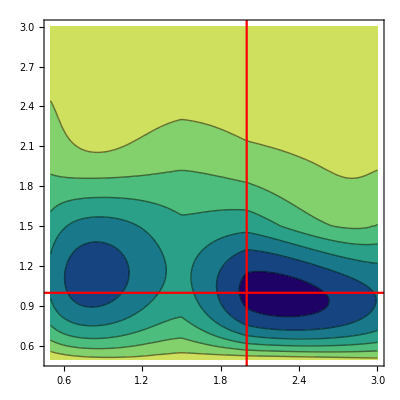

-Graphics-

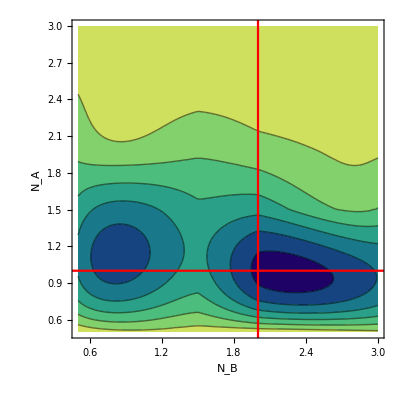

```mathematica
Show[%24,FrameLabel->{{HoldForm[Subscript[N, A]],None},{HoldForm[Subscript[N, B]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0]}]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter3/misfit_nanb.pdf",%27]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter3/misfit_nanb.pdf

```mathematica
ab[[Position[ab,Min[ab]][[1,1]]]]
```

{1,0.5,-3.82316×10^16}

```mathematica
Plot3D[Interpolation[ab,InterpolationOrder->3][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]
```

-Graphics3D-

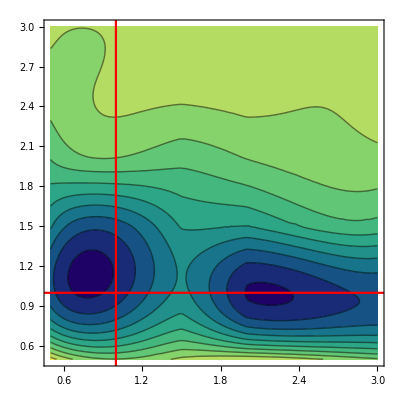

```mathematica
GraphicsRow[{Plot3D[Interpolation[ab,InterpolationOrder->3][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{1,y},{y,Range[0,5.5,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]]}]
```

```mathematica
Show[ContourPlot[Interpolation[ab][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],ListLinePlot[{Table[{1,y},{y,Range[0,5.5,0.075]}],Table[{y,1},{y,Range[00,3.05,0.001]}]},PlotStyle->{{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red},{Dashing[{0.01,1*^-2,0.01,1*^-2}],Red}}]]
```

-Graphics-

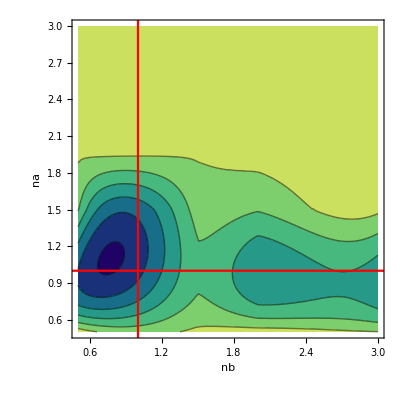

```mathematica
Show[%89,FrameLabel->{{HoldForm[na],None},{HoldForm[nb],None}},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

```mathematica
ef= ParallelTable[misfit[0.3,0.9,0.9,1.48],1000]
```

{1}
 |  |  |  |

```mathematica
Table[Plot3D[Interpolation[ef[[x]]][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],{x,1000}]
```

```mathematica
Table[ContourPlot[Interpolation[ef[[x]]][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],{x,1000}]
```

```mathematica
Plot3D[Interpolation[%183][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->Red]
```

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25]
```

```mathematica
Show[Plot3D[Interpolation[%149][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},PlotStyle->Directive[Black,Specularity[White,40]]],Plot3D[Interpolation[ef[[4]]][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]],Plot3D[Interpolation[ef[[1]]][x,y],{x,0.5,3.},{y,0.5,3.}
,Axes->{True,True,False},PlotStyle->Directive[Orange,Specularity[White,40]]],PlotRange->All]
```

```mathematica
Show[%173,ViewPoint->{0,0,-∞}]
```

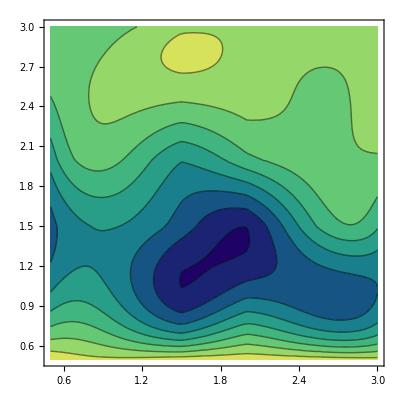

```mathematica
Show[ContourPlot[Interpolation[%65][b,y],{b,0.5,3.},{y,0.5,3.},FrameTicks->{{Automatic,None},{Automatic,None}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]]
```

```mathematica
ListPlot3D[%65,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}]]
```

```mathematica
Show[%86,ViewPoint->{0,∞,0}]
```

```mathematica
Show[%86,Lighting->Automatic]
```

```mathematica
ab=misfit[0.3,0.9,0.9,1.48]
Position[ab,Min[Transpose[ab][[3]]]]
```

{{0.5,0.5,-1.05534×10^12},{0.5,1,-9.59077×10^12},{0.5,1.5,-6.39501×10^12},{0.5,2,-3.73722×10^12},{0.5,2.5,-2.50167×10^12},{0.5,3,-1.92075×10^12},{1,0.5,-3.58161×10^12},{1,1,-1.10403×10^13},{1,1.5,-1.10514×10^13},{1,2,-2.80354×10^12},{1,2.5,-1.80081×10^12},{1,3,-2.01543×10^12},{1.5,0.5,-2.33992×10^12},{1.5,1,-7.4013×10^12},{1.5,1.5,-6.19383×10^12},{1.5,2,-3.94951×10^12},{1.5,2.5,-1.74272×10^12},{1.5,3,-1.36903×10^12},{2,0.5,-1.85146×10^12},{2,1,-1.16158×10^13},{2,1.5,-7.3006×10^12},{2,2,-3.03601×10^12},{2,2.5,-1.66919×10^12},{2,3,-1.33971×10^12},{2.5,0.5,-2.64892×10^12},{2.5,1,-1.09028×10^13},{2.5,1.5,-4.40112×10^12},{2.5,2,-2.37549×10^12},{2.5,2.5,-2.01381×10^12},{2.5,3,-1.3181×10^12},{3,0.5,-3.70066×10^12},{3,1,-1.18592×10^13},{3,1.5,-4.11648×10^12},{3,2,-2.22708×10^12},{3,2.5,-1.56543×10^12},{3,3,-1.56321×10^12}}

{{32,3}}

```mathematica
Position[ab,Min[Transpose[ab][[3]]]][[1,1]]
```

32

```mathematica
Position[ab,Min[Transpose[ab][[3]]]][[1,1]]
```

32

```mathematica
{ab[[Position[ab,Min[Transpose[ab][[3]]]][[1,1]],1]],ab[[Position[ab,Min[Transpose[ab][[3]]]][[1,1]],2]]}
```

{3,1}

```mathematica
Interpolation[%65]
```

InterpolatingFunction[…]

```mathematica
Plot3D[Interpolation[%65][x,y],{x,0.5,3.},{y,0.5,3.},Axes->False]
```

-Graphics3D-

```mathematica
Show[%123,ViewPoint->{0,∞,0}]
```

-Graphics3D-

```mathematica
Show[%120,Boxed->False]
```

-Graphics3D-